## Generate training data for DCNN

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs, all 4 classes)

```mathematica
RandomRule[n_Integer,W_Integer,H_Integer]:=Image[1-CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{W,H}]
net[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
data[W_Integer,H_Integer,n_Integer]:=Table[RandomRule[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

### Functions for creating datasets (1D totalistic CAs)

#### k=3, r=1 totalistic (class 4 only)

```mathematica
gen3T [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data3T2[W_Integer,H_Integer,n_Integer]:=Table[gen3T[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

#### k=4, r=1 totalistic (class 4 only, 1 example)

```mathematica
gen4T [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data4T[W_Integer,H_Integer,n_Integer]:=Table[gen4T[1004600,W,H]->4,n]
```

#### k=2, r=2 totalistic (all 4 classes)

```mathematica
gen2r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data2r2c4[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4[W,H,n], data2r2c3[W,H,n],data2r2c2[W,H,n],data2r2c1[W,H,n]]
```

#### k=5, r=1 totalistic (class 4 only)

```mathematica
gen5T4 [p_Integer,W_Integer,H_Integer]:=Image[1-CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data5T4[n_Integer,W_Integer,H_Integer]:=Table[gen5T4[i,W,H]->4,{i,RandomChoice[{781130654,772514435,1151319452,309095787,880862046,973835714,779446817,345466505,535500975,793363571,1052373865,455984785,339227109,1050973846,513368817,91315820,113925357},n]}]
```

### Generate test datasets

#### k=2, r=2 non-totalistic

```mathematica
genk2r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak2r2[W_Integer,H_Integer,n_Integer]:=Table[genk2r2[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=3, r=2 totalistic

```mathematica
genk3r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak3r2[W_Integer,H_Integer,n_Integer]:=Table[genk3r2[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

#### k=4, r=1 totalistic

```mathematica
genk4r1 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak4r1[W_Integer,H_Integer,n_Integer]:=Table[genk4r1[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

#### k=4, r=2 totalistic

```mathematica
genk4r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak4r2[W_Integer,H_Integer,n_Integer]:=Table[genk4r2[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=5, r=1 totalistic

```mathematica
gen5T2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data5T2[n_Integer,W_Integer,H_Integer]:=Table[gen5T2[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

#### k=6, r=1 totalistic

```mathematica
gen6T [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {6,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data6T[n_Integer,W_Integer,H_Integer]:=Table[gen6T[i,W,H]->i,{i,RandomInteger[2821109907455,n]}]
```

## Sample training sets

### ECA training data (120x60 pixel images)

```mathematica
sampleECA=data[120,60,20]
```

{-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### k=2, r=2 totalistic (120x60 pixels, 3 images in each of the four classes)

```mathematica
genData2r2[120,60,5]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1}

#### k=3, r=1 totalistic (120x60 pixels, class 4 CAs only)

```mathematica
data3T2[120,60,20]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

#### k=4, r=1 totalistic (120x60 pixels, class 4 CA only, rule 1004600]

```mathematica
data4T[120,60,20]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

## Training a DCNN on ECA and Totalistic CA data

### Create DCNN

```mathematica
netECA=netTwoC[120,60]
```

NetChain[<>]

```mathematica
netECA2=netTwoC[120,60]
```

NetChain[<>]

#### Network III: bigger images, includes k=5, r=1 data

```mathematica
netECA3=netTwoC[200,120]
```

NetChain[<>]

### Create training data (combining ECAs, k=2, r=2 totalistic and k=3/4, r=1 totalistic)

```mathematica
dataECA=data[120,60,65536];
```

```mathematica
dataTotalistic2=genData2r2[120,60,2048];
```

```mathematica
dataTotalistic3=data3T2[120,60,8192];
```

```mathematica
dataTotalistic4=data4T[120,60,8192];
```

```mathematica
fullTrainingSet=Join[dataECA,dataTotalistic2, dataTotalistic3, dataTotalistic4];
Length[fullTrainingSet]
RandomSample[fullTrainingSet,10]
```

90112

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2}

### Create training data for Network III (ECAs; k=2,r=2; k=3, r=1; k=4, r=1; k=5, r=1)

```mathematica
dataECA3=data[200,120,65536];
dataTotalistic2Big=genData2r2[200,120,2048];
dataTotalistic3Big=data3T2[200,120,8192];
dataTotalistic4Big=data4T[200,120,8192];
dataTotalistic5Big=data5T4[8192,200,120];
fullTrainingBig=Join[dataECA3,dataTotalistic2Big,dataTotalistic3Big,dataTotalistic4Big,dataTotalistic5Big];
Length[fullTrainingBig]
RandomSample[fullTrainingBig,20]
```

98304

{-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→4}

### Train network

```mathematica
netECA=NetTrain[netECA,fullTrainingSet,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","WolframCAClassifier2"}]
```

NetChain[<>]

```mathematica
Export["netECA20may.wlnet",netECA,"WLNet"]
```

netECA20may.wlnet

```mathematica
netECA2=NetTrain[netECA2,fullTrainingSet,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","WolframCAClassifier2"}]
```

NetChain[<>]

```mathematica
netECA3=NetTrain[netECA3,fullTrainingBig,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","networkIII"}]
```

NetChain[<>]

```mathematica
Export["netECA3-21may.wlnet",netECA3,"WLNet"]
```

netECA3-21may.wlnet

### Generate test data

```mathematica
testDataECA=data[120,60,4096];
testData3T=data3T2[120,60,4096];
testData4T=data4T[120,60,4096];
fullTestSet=Join[testDataECA,testData3T,testData4T];
Length[fullTestSet]
```

12288

```mathematica
RandomSample[fullTestSet,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
NetMeasurements[netECA2,fullTestSet,"Accuracy"]
```

0.998698

```mathematica
NetMeasurements[netECA,fullTestSet,{"Precision","Recall"}]
```

{<|1→1.,2→0.999359,3→0.998102,4→1.|>,<|1→0.994444,2→1.,3→1.,4→0.999879|>}

### Generate test data for Network III

```mathematica
testDataECABig=data[200,120,4096];
testData3TBig=data3T2[200,120,4096];
testData4TBig=data4T[200,120,4096];
testData5TBig=data5T4[4096,200,120];
fullTestSetBig=Join[testDataECABig,testData3TBig,testData4TBig,testData5TBig];
Length[fullTestSetBig]
```

16384

```mathematica
RandomSample[fullTestSetBig,10]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2}

```mathematica
NetMeasurements[netECA3,fullTestSetBig,{"Accuracy","Precision","Recall"}]
```

{0.999939,<|1→1.,2→1.,3→0.998201,4→1.|>,<|1→1.,2→1.,3→1.,4→0.999919|>}

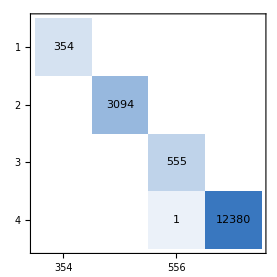
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[netECA3,fullTestSetBig,"ConfusionMatrixPlot"]
```

### Test on unseen CA data

#### Testing k=2, r=2 non-totalistic examples

```mathematica
testDatak2r2=datak2r2[120,60,1024];
```

```mathematica
testk2r2=RandomSample[testDatak2r2, 10];
Thread[testk2r2->netECA2[Keys@testk2r2]]
```

{(-Graphics-→1300870680)→3,(-Graphics-→587192303)→2,(-Graphics-→1859315079)→3,(-Graphics-→737180880)→4,(-Graphics-→2079513555)→3,(-Graphics-→3419491851)→3,(-Graphics-→567693458)→4,(-Graphics-→3890050526)→2,(-Graphics-→2560131967)→3,(-Graphics-→1412343793)→4}

#### Testing k=5, r=1 totalistic examples

```mathematica
testSet5T= data5T2[10,120,60];
```

```mathematica
Thread[testSet5T->netECA2[Keys@testSet5T]]
```

{(-Graphics-→1115739301)→3,(-Graphics-→104465240)→4,(-Graphics-→1010395314)→4,(-Graphics-→343019604)→4,(-Graphics-→816981792)→4,(-Graphics-→755606148)→3,(-Graphics-→1113703737)→4,(-Graphics-→175189303)→3,(-Graphics-→704478691)→4,(-Graphics-→459024141)→4}

#### Testing k=3, r=2 totalistic examples

```mathematica
testDatak3r2=datak3r2[120,60,10];
Thread[testDatak3r2->netECA2[Keys@testDatak3r2]]
```

{(-Graphics-→33024)→4,(-Graphics-→160970)→4,(-Graphics-→170691)→4,(-Graphics-→112352)→4,(-Graphics-→159078)→4,(-Graphics-→150457)→3,(-Graphics-→89209)→4,(-Graphics-→78995)→3,(-Graphics-→125123)→3,(-Graphics-→72936)→3}

```mathematica
newTestDatak3r2=datak3r2[120,60,10];
Thread[newTestDatak3r2->netECA2[Keys@newTestDatak3r2]]
```

{(-Graphics-→140106)→4,(-Graphics-→163339)→4,(-Graphics-→155653)→2,(-Graphics-→131345)→4,(-Graphics-→21761)→3,(-Graphics-→140798)→4,(-Graphics-→59961)→4,(-Graphics-→173143)→1,(-Graphics-→100340)→4,(-Graphics-→153082)→1}

#### Testing k=4, r=1 totalistic examples

```mathematica
testData4kr1 = datak4r1[120,60,10];
k4r1test=Thread[testData4kr1->netECA2[Keys@testData4kr1]]
```

{(-Graphics-→409248)→4,(-Graphics-→461362)→4,(-Graphics-→791752)→4,(-Graphics-→518234)→2,(-Graphics-→268080)→4,(-Graphics-→75543)→4,(-Graphics-→814528)→4,(-Graphics-→399029)→4,(-Graphics-→594775)→4,(-Graphics-→597159)→4}

#### Testing on k=3, r=1 totalistic code 1599 (class 4)

```mathematica
code1599table= Thread[Table[Image[CellularAutomaton[{2007, {3,1}},RandomInteger[1,120],60],ImageSize->{120,60}]->4,{n,0,1000}]];
NetMeasurements[netECA2,code1599table,"Accuracy"]
```

1.

```mathematica
sample1599=Keys@RandomSample[code1599table,10];
Thread[sample1599->netECA2[sample1599]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking highest-entropy and lowest-entropy predictions in test set

```mathematica
entropyImages=RandomSample[Keys[fullTestSet],5000];
entropies=netECA2[entropyImages,"Entropy"];
highEnt=entropyImages[[Ordering[entropies,-10]]]
lowEnt=entropyImages[[Ordering[entropies,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEnt->netECA2[highEnt]]
Thread[lowEnt->netECA2[lowEnt]]
```

{-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking highest- and lowest-entropy images in test set for Network III

```mathematica
entropyImagesBig=RandomSample[Keys[fullTestSetBig],5000];
entropiesBig=netECA3[entropyImagesBig,"Entropy"];
highEntBig=entropyImagesBig[[Ordering[entropiesBig,-10]]]
lowEntBig=entropyImagesBig[[Ordering[entropiesBig,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBig->netECA3[highEntBig]]
Thread[lowEntBig->netECA3[lowEntBig]]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Testing Network III on k=6, r=1 images

```mathematica
netECA3=Import["netECA3-21may.wlnet","WLNet"]
```

NetChain[<>]

```mathematica
random6T=RandomInteger[2821109907455];
netECA3[gen6T[random6T,200,120]]
```

4

```mathematica
testData6kr1 = data6T[4,200,120];
k6r1test=Thread[Keys@testData6kr1->netECA3[Keys@testData6kr1]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1}

## Reshape network to take any size CA image

```mathematica
SetDirectory[NotebookDirectory[]];
netECA=Import["trained2c2.wlnet","WLNet"]
```

NetChain[<>]

```mathematica
netResizeECA[W_,H_]:=NetChain[{ConvolutionLayer[16,{2,3},"Weights"->NetExtract[netECA2,{"conv1","Weights"}],"Biases"->NetExtract[netECA2,{"conv1","Biases"}]],Ramp,ConvolutionLayer[16,{2,3},"Weights"->NetExtract[netECA2,{"conv3","Weights"}],"Biases"->NetExtract[netECA2,{"conv3","Biases"}]],Ramp,PoolingLayer[{H,W}-{2,4}],FlattenLayer[],NetExtract[netECA2,"linear"],NetExtract[netECA2,"linear2"],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
bigNet=netResizeECA[300,150]
```

NetChain[<>]

#### Test accuracy on 300x150 ECA images

```mathematica
bigCA=data[300,150,1024];
NetMeasurements[bigNet,bigCA,"Accuracy"]
```

0.999023

```mathematica
sampleBigCA=Keys@RandomSample[bigCA,10];
Thread[sampleBigCA->bigNet[sampleBigCA]]
```

{-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2}

## Feature Space Plots and Visualisations

```mathematica
FeatureSpacePlot[RandomSample[Keys@dataECA,50],FeatureExtractor->netECA2, LabelingFunction->Callout, LabelingSize->90,ImageSize->Large]
```

-Graphics-

```mathematica
FeatureSpacePlot[RandomSample[Keys@dataTotalistic2,50],FeatureExtractor->netECA2, LabelingFunction->Callout, LabelingSize->90,ImageSize->Large]
```

-Graphics-

```mathematica
FeatureSpacePlot[RandomSample[Keys@fullTestSet,50],FeatureExtractor->netECA2, LabelingFunction->Callout, LabelingSize->90,ImageSize->Large]
```

-Graphics-

```mathematica
NetMeasurements[netECA2,fullTestSet,"Accuracy"]
```

0.998698

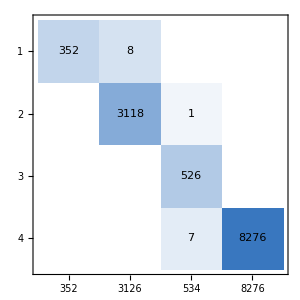
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[netECA2,fullTestSet,"ConfusionMatrixPlot"]
```

### Plotting mean activations of convolutional layer filters

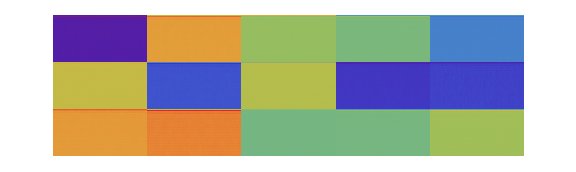

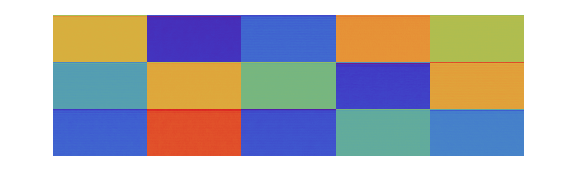

```mathematica
activations1=NetMeasurements[netECA,fullTestSet,NetPort[{1,"Output"}]];
activations3=NetMeasurements[netECA,fullTestSet,NetPort[{3,"Output"}]];
ArrayPlot[ArrayFlatten@Partition[activations1,5],ColorFunction->"Rainbow",FrameTicks->None,ImageSize->Large]
ArrayPlot[ArrayFlatten@Partition[activations3,5],ColorFunction->"Rainbow",FrameTicks->None,ImageSize->Large]
```

### Checking net certainty on test set and unseen rules

```mathematica
sampleSmall=RandomSample[fullTestSet,20];
Thread[Keys@sampleSmall->netECA2[Keys@sampleSmall,{"TopProbabilities",2}]]
```

{-Graphics-→{3→0.00112124,2→0.998786},-Graphics-→{3→4.18814×10^-6,2→0.999996},-Graphics-→{3→6.15553×10^-6,2→0.999994},-Graphics-→{1→5.26989×10^-6,2→0.999995},-Graphics-→{3→5.20857×10^-16,4→1.},-Graphics-→{3→5.7411×10^-14,4→1.},-Graphics-→{3→6.69613×10^-17,4→1.},-Graphics-→{3→0.000167213,4→0.999833},-Graphics-→{2→0.0638157,1→0.936184},-Graphics-→{2→1.6293×10^-6,1→0.999998},-Graphics-→{3→3.71125×10^-8,2→1.},-Graphics-→{3→2.18475×10^-8,4→1.},-Graphics-→{3→0.000149614,4→0.99985},-Graphics-→{3→0.000141582,4→0.999858},-Graphics-→{2→0.0655017,3→0.934498},-Graphics-→{3→2.62035×10^-9,2→1.},-Graphics-→{3→0.000433412,4→0.999567},-Graphics-→{3→1.18482×10^-9,2→1.},-Graphics-→{1→0.000107818,2→0.999891},-Graphics-→{3→1.01963×10^-15,4→1.}}

```mathematica
sampleProbs=RandomSample[bigCA,20];
Thread[Keys@sampleProbs->bigNet[Keys@sampleProbs,{"TopProbabilities",2}]]
```

{-Graphics-→{3→3.89001×10^-9,2→1.},-Graphics-→{3→0.000108923,2→0.999891},-Graphics-→{2→0.0385769,1→0.961423},-Graphics-→{3→4.15606×10^-6,2→0.999996},-Graphics-→{1→4.40941×10^-6,2→0.999996},-Graphics-→{1→0.000266148,2→0.999732},-Graphics-→{3→1.44089×10^-6,2→0.999999},-Graphics-→{4→0.0000156771,2→0.999983},-Graphics-→{3→1.78626×10^-6,2→0.999998},-Graphics-→{2→0.0364814,3→0.962053},-Graphics-→{4→0.0000213186,2→0.999974},-Graphics-→{1→4.07375×10^-10,2→1.},-Graphics-→{3→0.0504669,2→0.946138},-Graphics-→{2→0.0127308,1→0.987269},-Graphics-→{3→7.67513×10^-10,2→1.},-Graphics-→{3→0.000231599,2→0.99966},-Graphics-→{3→2.91542×10^-6,2→0.999997},-Graphics-→{4→0.000227393,3→0.99977},-Graphics-→{1→9.47213×10^-8,2→1.},-Graphics-→{2→0.0226383,3→0.97733}}

```mathematica
sampleProbs3T=Keys@RandomSample[code1599table,20];
Thread[sampleProbs3T->netECA2[sampleProbs3T,{"TopProbabilities",2}]]
```

{-Graphics-→{3→0.0000155222,4→0.999985},-Graphics-→{3→1.05313×10^-9,4→1.},-Graphics-→{3→1.41086×10^-10,4→1.},-Graphics-→{3→7.87203×10^-11,4→1.},-Graphics-→{3→3.57163×10^-8,4→1.},-Graphics-→{3→7.91801×10^-6,4→0.999987},-Graphics-→{1→0.000200531,4→0.999799},-Graphics-→{3→5.73903×10^-8,4→1.},-Graphics-→{3→4.25244×10^-8,4→1.},-Graphics-→{3→7.77643×10^-8,4→1.},-Graphics-→{3→1.59286×10^-9,4→1.},-Graphics-→{3→1.38673×10^-8,4→1.},-Graphics-→{3→0.0000575239,4→0.999907},-Graphics-→{3→1.42931×10^-8,4→1.},-Graphics-→{3→2.32912×10^-7,4→1.},-Graphics-→{3→2.99479×10^-7,4→1.},-Graphics-→{3→2.54952×10^-8,4→1.},-Graphics-→{3→1.81434×10^-7,4→1.},-Graphics-→{3→1.11816×10^-6,4→0.999999},-Graphics-→{3→1.2536×10^-9,4→1.}}

```mathematica
sampleProbs4T=datak4r1[120,60,20];
Thread[sampleProbs4T->netECA2[Keys@sampleProbs4T,{"TopProbabilities",2}]]
```

{(-Graphics-→792653)→{3→2.61782×10^-17,4→1.},(-Graphics-→990824)→{3→4.00659×10^-6,4→0.999996},(-Graphics-→987727)→{3→1.41622×10^-14,4→1.},(-Graphics-→16099)→{4→0.000315189,3→0.999685},(-Graphics-→437825)→{2→0.0180752,3→0.97727},(-Graphics-→913979)→{3→4.46037×10^-8,4→1.},(-Graphics-→385055)→{3→3.04379×10^-11,4→1.},(-Graphics-→220630)→{4→0.34321,3→0.656253},(-Graphics-→915633)→{2→1.20232×10^-12,4→1.},(-Graphics-→646026)→{4→1.01234×10^-7,2→1.},(-Graphics-→626652)→{3→3.07408×10^-12,4→1.},(-Graphics-→269656)→{3→3.39499×10^-6,4→0.999997},(-Graphics-→108564)→{4→0.00591701,3→0.992707},(-Graphics-→954410)→{4→8.03653×10^-8,3→1.},(-Graphics-→826457)→{3→0.0563516,4→0.943648},(-Graphics-→119543)→{3→0.040927,4→0.959073},(-Graphics-→548647)→{3→0.0000398692,4→0.99996},(-Graphics-→279497)→{3→0.000142115,4→0.999858},(-Graphics-→179255)→{3→0.000130573,4→0.999869},(-Graphics-→870675)→{3→1.36294×10^-15,4→1.}}

## Visualising Network Internals

### Second convolutional layer

```mathematica
layer=NetExtract[netECA2,"conv3"]
kernels=NetExtract[layer,"Weights"];
Map[ImageAdjust@Image[#,Interleaving->False]&,Normal@kernels]
```

ConvolutionLayer[<>]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
takeLayer="conv3";
channel=1;
featureNet=NetAppend[NetTake[netECA2,takeLayer],"L2_norm"->{PartLayer[{channel}],ElementwiseLayer[x↦x^2],SummationLayer[]}]
```

NetChain[<>]

```mathematica
img1=Image[CellularAutomaton[30,RandomInteger[1,120],60]]
```

-Graphics-

```mathematica
Image[Normalize[Normal@featureNet[img,NetPortGradient["Input"]],array↦8 Max@Abs@Flatten[array]],Interleaving->False]
```

-Graphics-

```mathematica
jitter[{dx_,dy_}][img_Image]:=ImagePad[img,{dx {1,-1},dy {1,-1}},"Periodic"]
```

```mathematica
Do[offset=RandomInteger[{-8,8},{2}];
img1=ImageClip@ImageAdd[img1,jitter[-offset][Image[Normalize[featureNet[jitter[offset][img1],NetPortGradient["Input"]],array↦8 Max@Abs@Flatten[array]],Interleaving->False]]],{n,2048}]
```

```mathematica
img1
```

-Graphics-

```mathematica
img2
```

-Graphics-

```mathematica
img3
```

-Graphics-

```mathematica
img4
```

-Graphics-

```mathematica
img5
```

-Graphics-

```mathematica
img6
```

-Graphics-

```mathematica
img7
```

-Graphics-

```mathematica
img8
```

-Graphics-

```mathematica
img9
```

-Graphics-

```mathematica
img10
```

-Graphics-

```mathematica
img11
```

-Graphics-

```mathematica
img12
```

-Graphics-

```mathematica
img13
```

-Graphics-

```mathematica
img14
```

-Graphics-

```mathematica
img15
```

-Graphics-

```mathematica
img16
```

-Graphics-

```mathematica
GraphicsGrid[{{img1,img2,img3,img4},{img5,img6,img7,img8},{img9,img10,img11,img12},{img13,img14,img15,img16}}, ImageSize->Full]
```

-Graphics-

```mathematica
Export["/Users/thorsilver/Documents/conv layer 2.png",%1184,"PNG"]
```

/Users/thorsilver/Documents/conv layer 2.png

### First convolutional layer

```mathematica
layer=NetExtract[netECA2,"conv1"]
kernels=NetExtract[layer,"Weights"];
Map[ImageAdjust@Image[#,Interleaving->False]&,Normal@kernels]
```

ConvolutionLayer[<>]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
takeLayer2="conv1";
channel=16;
featureNet2=NetAppend[NetTake[netECA2,takeLayer2],"L2_norm"->{PartLayer[{channel}],ElementwiseLayer[x↦x^2],SummationLayer[]}]
```

NetChain[<>]

```mathematica
imgc16=Image[CellularAutomaton[30,RandomInteger[1,120],60]]
```

-Graphics-

```mathematica
jitter[{dx_,dy_}][img_Image]:=ImagePad[img,{dx {1,-1},dy {1,-1}},"Periodic"]
```

```mathematica
Do[offset=RandomInteger[{-8,8},{2}];
imgc16=ImageClip@ImageAdd[imgc16,jitter[-offset][Image[Normalize[featureNet2[jitter[offset][imgc16],NetPortGradient["Input"]],array↦8 Max@Abs@Flatten[array]],Interleaving->False]]],{n,2048}]
```

```mathematica
imgc1
```

-Graphics-

```mathematica
imgc2
```

-Graphics-

```mathematica
imgc3
```

-Graphics-

```mathematica
imgc4
```

-Graphics-

```mathematica
imgc5
```

-Graphics-

```mathematica
imgc6
```

-Graphics-

```mathematica
imgc7
```

-Graphics-

```mathematica
imgc8
```

-Graphics-

```mathematica
imgc9
```

-Graphics-

```mathematica
imgc10
```

-Graphics-

```mathematica
imgc11
```

-Graphics-

```mathematica
imgc12
```

-Graphics-

```mathematica
imgc13
```

-Graphics-

```mathematica
imgc14
```

-Graphics-

```mathematica
imgc15
```

-Graphics-

```mathematica
imgc16
```

-Graphics-

```mathematica
GraphicsGrid[{{imgc1,imgc2,imgc3,imgc4},{imgc5,imgc6,imgc7,imgc8},{imgc9,imgc10,imgc11,imgc12},{imgc13,imgc14,imgc15,imgc16}}, ImageSize->Full]
```

-Graphics-

```mathematica
Export["/Users/thorsilver/Documents/conv layer 1.png",%1265,"PNG"]
```

/Users/thorsilver/Documents/conv layer 1.png